# Global Cellular Automata

## How do diseases spread over long distances?

### Introduction

We’ve seen how diseases can spread using a simple cellular automaton, where cells can infect adjacent cells. But what happens when we want to model the dynamics of an infectious disease over a large distance? Supposedly, a cell might still be able to infect other cells that are farther away than its immediate neighbours. It may not have such a profound effect on these cells, but it would have an effect nonetheless.

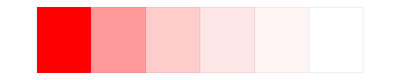
-Graphics-The red cell on the left can infect far-away cells, but the effect diminishes with distance.

```mathematica
Labeled[ArrayPlot[{Table[1/i,{i,1,6}]},ColorFunction->(RGBColor[1,1-#,1-#,1]&),Frame->False,Mesh->True,MeshStyle->RGBColor[0.5,0.5,0.5,0.1]],
"The red cell on the left can infect far-away cells, but the effect diminishes with distance."//Text]
```

So how would we define a function that computes the effect one cell has another? One way would be to make the effect strength inversely proportional to the distance between two cells:

```mathematica
effectStrength[{x1_,y1_},{x2_,y2_}]:=1/(√((x1-x2)^2+(y1-y2)^2));
```

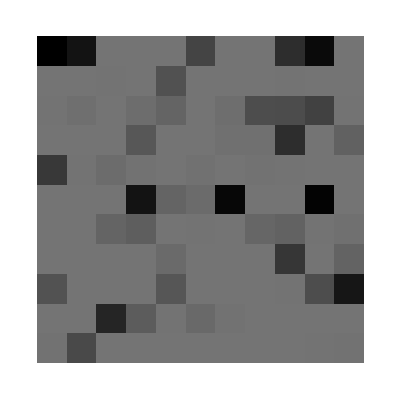

```mathematica
SetDirectory[NotebookDirectory[]];
<< "DiseaseLibrary.wl";

pop=RandomReal[1,{50,50}]^7*0.5+0.5;
globalNeighbours=Function[{matrix, row, col},
mForEachInMatrix[matrix,Function[{otherCell,otherCoords},
If[col==otherCoords[[2]]&&row==otherCoords[[1]],
0,
pop[[row,col]]*pop[[otherCoords[[1]],otherCoords[[2]]]]*otherCell*effectStrength[{col,row},{otherCoords[[2]],otherCoords[[1]]}]
]
]
]//Flatten
];

α=0.2; (* Infectivity *)
δ=0.5; (* Clearance rate *)
mCellNextState=Function[{cell,neighbors},
δ cell+α Total[neighbors]
];

matrix=ConstantArray[0,{11,11}];
matrix[[6,6]]=1;
iterations=10;
results=mRunModel[matrix,mCellNextState,globalNeighbours,iterations];
ArrayPlot[pop[[1;;11,1;;11]]]
ListAnimate[Map[ArrayPlot[#,ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->True,MeshStyle->RGBColor[0.5,0.5,0.5,0.2]]&,results],AnimationRunning->False,Frame->False]
```